```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\fluc_T\fluctuations_T\highorder_2p1\input_h\finitemub\mub100\data

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

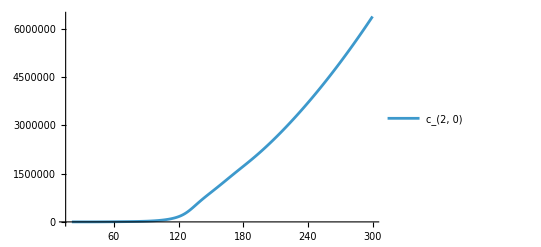

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
T=Flatten[Table[21+(i-1),{i,1,280}]];
ListLinePlot[Transpose[{T,chi2}],PlotRange->All,PlotLegends->{"c_(2, 0)"}]
```

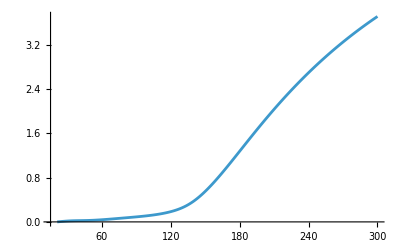

```mathematica
ListLinePlot[Transpose[{T,(chi0-chi0[[1]])/T^4}],PlotRange->All]
```

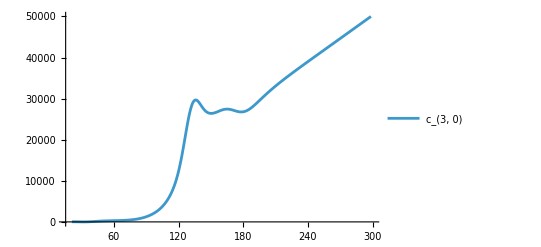

```mathematica
ListLinePlot[Transpose[{T,chi3}],PlotRange->{All,{-0000,50000}},PlotLegends->{"c_(3, 0)"}]
```

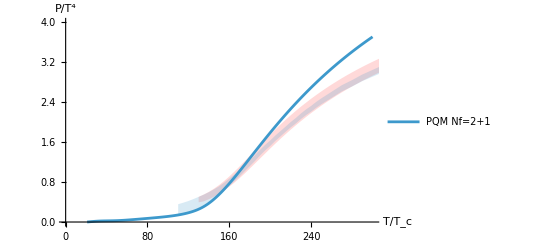

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T/1,(chi0-chi0[[1]])/T^4}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","P/T^4"}]
```

### Plot

ListLinePlot::lpn: {{},{{130.,0.395},«49»,«5»},{{130.,0.504},{135.,0.55},{140.,0.604},{145.,0.668},{150.,0.74},{155.,0.823},{160.,0.913},{165.,1.01},{170.,1.112},{175.,1.218},{180.,1.326},{185.,1.435},«27»,{325.,3.436},{330.,3.475},{335.,3.514},{340.,3.552},{345.,3.588},{350.,3.623},{355.,3.656},{360.,3.689},{365.,3.72},{370.,3.751},{375.,3.781},«5»}} 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 … 中的图形对象.

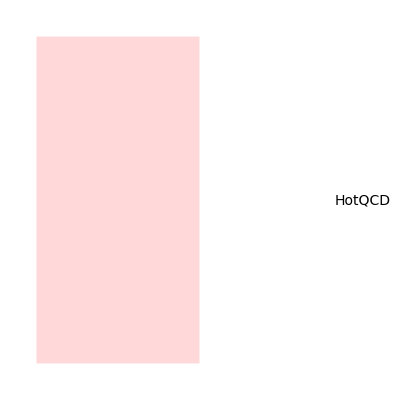
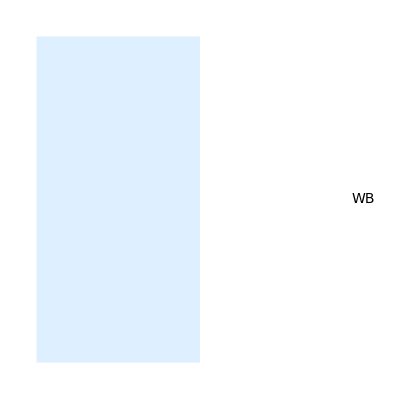
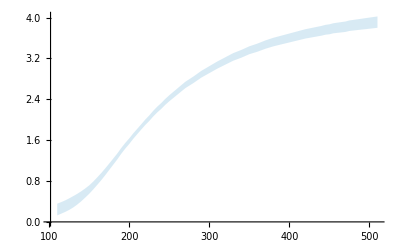
Show[ListLinePlot[{c0,{{130.,0.395},{135.,0.414},{140.,0.457},{145.,0.508},{150.,0.566},{155.,0.633},{160.,0.708},{165.,0.79},{170.,0.879},{175.,0.973},{180.,1.071},{185.,1.172},{190.,1.272},{195.,1.373},{200.,1.473},{205.,1.571},{210.,1.667},{215.,1.76},{220.,1.851},{225.,1.938},{230.,2.023},{235.,2.105},{240.,2.184},{245.,2.259},{250.,2.333},{255.,2.403},{260.,2.47},{265.,2.536},{270.,2.599},{275.,2.66},{280.,2.718},{285.,2.774},{290.,2.829},{295.,2.881},{300.,2.932},{305.,2.981},{310.,3.028},{315.,3.073},{320.,3.117},{325.,3.16},{330.,3.2},{335.,3.239},{340.,3.278},{345.,3.315},{350.,3.351},{355.,3.385},{360.,3.418},{365.,3.451},{370.,3.482},{375.,3.513},{380.,3.541},{385.,3.569},{390.,3.597},{395.,3.623},{400.,3.65}},{{130.,0.504},{135.,0.55},{140.,0.604},{145.,0.668},{150.,0.74},{155.,0.823},{160.,0.913},{165.,1.01},{170.,1.112},{175.,1.218},{180.,1.326},{185.,1.435},{190.,1.542},{195.,1.649},{200.,1.754},{205.,1.856},{210.,1.953},{215.,2.048},{220.,2.139},{225.,2.227},{230.,2.312},{235.,2.392},{240.,2.471},{245.,2.546},{250.,2.618},{255.,2.688},{260.,2.755},{265.,2.819},{270.,2.882},{275.,2.942},{280.,2.999},{285.,3.055},{290.,3.109},{295.,3.161},{300.,3.211},{305.,3.259},{310.,3.306},{315.,3.35},{320.,3.394},{325.,3.436},{330.,3.475},{335.,3.514},{340.,3.552},{345.,3.588},{350.,3.623},{355.,3.656},{360.,3.689},{365.,3.72},{370.,3.751},{375.,3.781},{380.,3.808},{385.,3.836},{390.,3.862},{395.,3.888},{400.,3.914}}},Filling→{2→{3}},FillingStyle→RGBColor[1, 0.85, 0.85],PlotStyle→{Automatic,None,None},PlotLegends→{PQM Nf=2+1},PlotRange→{{0.4,1.6},{0,3}}],-Graphics-,-Graphics-,-Graphics-,AxesLabel→{T/T_c,P/T^4}]

```mathematica
PlotP=Show[ListLinePlot[{c0,Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,3}}],Graphics[{Text[Style["HotQCD",14],{0.9,2.5}],LightRed,Rectangle[{0.5,2.3},{0.7,2.7}]}],Graphics[{Text[Style["WB",14],{0.9,1.8}],LightBlue,Rectangle[{0.5,1.6},{0.7,2.}]}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}}(*,FillingStyle->LightBlue*),PlotStyle->{None,None}],AxesLabel->{"T/T_c","P/T^4"}]
```

```mathematica
Plotcs2=Show[ListLinePlot[{cs2},FillingStyle->LightRed,PlotStyle->{Automatic,Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,0.4}}],ListLinePlot[{WBcsdown,WBcsup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","(c^2)_s"}]
```

-Graphics-

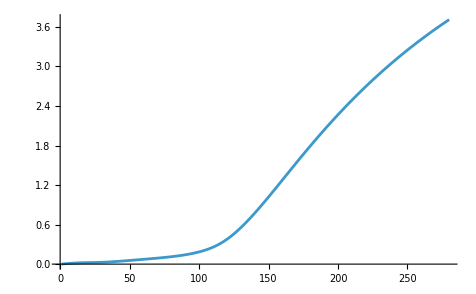

```mathematica
plotc0=ListLinePlot[chi0/T^4]
```

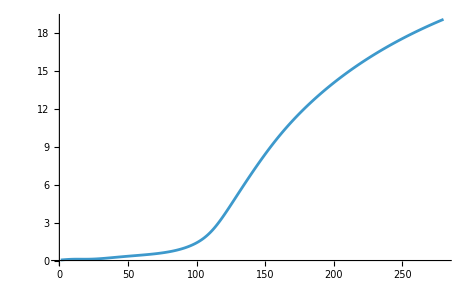

```mathematica
plotc1=ListLinePlot[chi1/T^3]
```

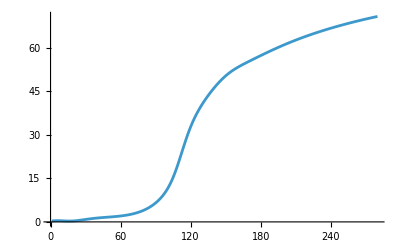

```mathematica
plotc2=ListLinePlot[chi2/T^2]
```

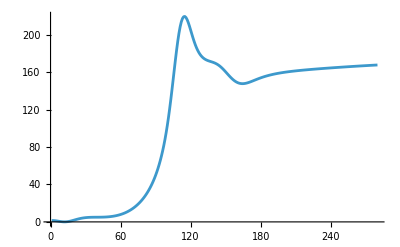

```mathematica
plotc3=ListLinePlot[chi3/T]
```

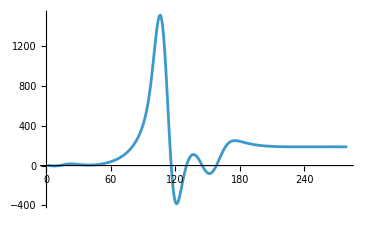

```mathematica
plotc4=ListLinePlot[chi4,PlotRange->All]
```

```mathematica
Export["./PoT4.pdf",PlotP];
Export["./cs2.pdf",Plotcs2];
Export["./c1.pdf",plotc1];
Export["./c2.pdf",plotc2];
Export["./c3.pdf",plotc3];
Export["./c4.pdf",plotc4];
```

## Temperature Fluctuations

```mathematica
c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
c5=T^11(-15(1/chi2)^7(chi3)^3-(1/chi2)^5 chi5+10(1/chi2)^6 chi3 chi4);
c6=T^14(105(1/chi2)^9 chi3^4-105(1/chi2)^8 chi3^2 chi4+10(1/chi2)^7 chi4^2+15(1/chi2)^7 chi3 chi5-(1/chi2)^6 chi6);
Export["./c2.dat",c2];
Export["./c3.dat",c3];
Export["./c4.dat",c4];
Export["./c5.dat",c5];
Export["./c6.dat",c6];
```

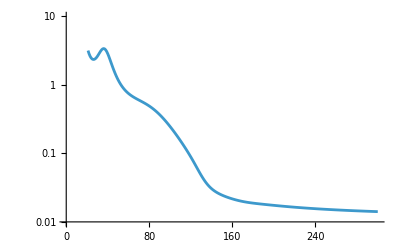

```mathematica
ListLinePlot[Transpose[{T,c2}],PlotRange->{{0,300},{0.01,10}},ScalingFunctions->"Log"]
```

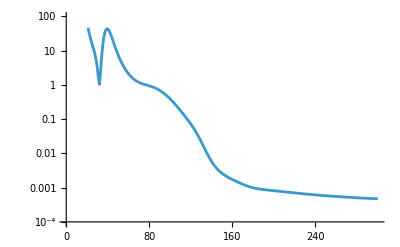

```mathematica
ListLinePlot[Transpose[{T,-c3}],PlotRange->{{0,300},{100,0.0001}},ScalingFunctions->"Log"]
```

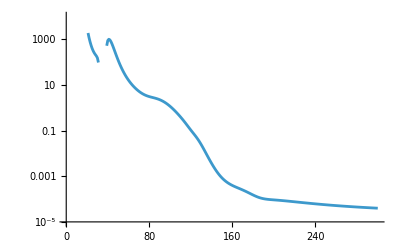

```mathematica
ListLinePlot[Transpose[{T,c4}],PlotRange->{{0,300},{0.00001,10000}},ScalingFunctions->"Log"]
```

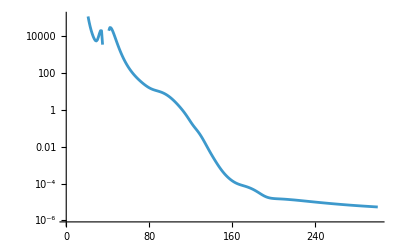

```mathematica
ListLinePlot[Transpose[{T,-c5}],PlotRange->{{0,300},All},ScalingFunctions->"Log"]
```

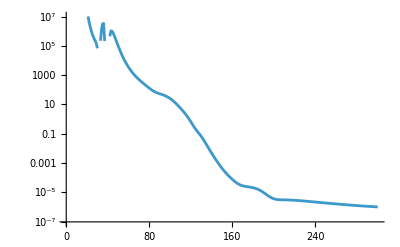

```mathematica
ListLinePlot[Transpose[{T,c6}],PlotRange->{{0,300},All},ScalingFunctions->"Log"]
```